```mathematica
(* Initialization file necessary for running the Manipulate notebooks *)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Get["../../CoreCode/Autoload/init.m"];
Get["../../CoreCode/MakeAnalyticalResults.m"];
Get["../../CoreCode/VarsAndFuncs.m"];
Get["../../CoreCode/DrawDiagrams.m"];
ω=(ρ-1)/2;
γ=𝔤+℧;
VerboseOutput=False;
κU=((κ /. Severance ->0) /. PDies -> 0) /. τ -> 0;
```

```mathematica
({ζ Γ,R κU (1+(ÞΓ^-ρ-1)/℧)^(1/ρ),R κU (1+ℵ)^(1/ρ)} /. PDies -> 0)
```

{(1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ),(1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ),(1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)}

```mathematica
((𝒷E /. Severance ->0) /. PDies -> 0) /. τ -> 0
```

1/(1+𝔤)(1+r) ((1+((1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))/(1-((1+r) (1-℧))/(1+𝔤)+((1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))-((1-(1+𝔤)/((1+r) (1-℧))) (1+((1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)))/(1-((1+r) (1-℧))/(1+𝔤)+((1+r) (1-((1+r)/(1+ϑ))^(1/ρ)/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))-(1+𝔤)/((1+r) (1-℧))) (1-℧)

```mathematica
{ϑ,ρ,Severance,PDies,℧,τ}={0.03,2,0,0,0.005,0};
Print[
MatrixForm[ResultsByGandR=(({({𝒷E,1/(1-Γ/R),(ÞΓ-1),R/Γ-1 }/. 𝔤 -> {0.025,0.02})/. r -> {0.035,0.045,0.055}})[[1]]),1]];
{𝒷EHi,𝒷ELo,HWHi,HWLo,þgHi,þgLo,rMγHi,rMγLo}=Flatten[ResultsByGandR,1];Print[MatrixForm[Transpose[{𝒷EHi/Total[𝒷EHi],𝒷ELo/Total[𝒷ELo]}]]]
```

((9.49443
9.88912
10.7436) | (11.0146
11.8826
13.7007)
(213.435
70.3739
42.456) | (104.817
52.5803
35.3146)
(-0.026915
-0.0222254
-0.0175582) | (-0.022145
-0.0174324
-0.0127423)
(0.00470732
0.0144146
0.024122) | (0.00963235
0.0193873
0.0291422))

(0.315146 | 0.300963
0.328246 | 0.324679
0.356608 | 0.374358)

```mathematica
{ρ^-1(r - ϑ) - γ,r-γ}={impatience,temptation}
```

```mathematica
ClearAll[ϑ];ÞΓ
```

(0.995 √((1+r)/(1+ϑ)))/(1+𝔤)

```mathematica
ParametricPlot3D[((({r,(1-ÞΓ)^-1,𝒷E} )/. 𝔤->0.025))/. r ->rIndex /. ϑ->ϑIndex,{ϑIndex,0.,0.05},{rIndex,0.04,0.08}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[(({r,(1-ÞΓ)^-1,𝒷E} /. r ->rIndex)/. 𝔤->0.025)/. ϑ->ϑIndex,{ϑIndex,0.,0.05,0.005},{rIndex,0.04,0.08,0.005}],PlotRange->All]
```

-Graphics3D-

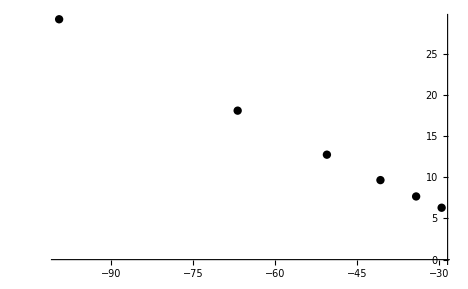

```mathematica
ListPlot[Transpose[(({(ÞΓ-1)^-1,𝒷E} /. r ->0.04)/. 𝔤->0.025)/. ϑ->{0.0,0.01,0.02,0.03,0.04,0.05}]]
```

```mathematica
{𝒷EHi,𝒷ELo,HWHi,HWLo,þgHi,þgLo,rMγHi,rMγLo}=Flatten[ResultsByGandR,1];{𝒷EHi/Total[𝒷EHi],𝒷ELo/Total[𝒷ELo]}
```

{{0.248889,0.286456,0.464656},{0.16322,0.229408,0.607372}}

```mathematica
{𝒷EHi/Total[𝒷EHi],𝒷ELo/Total[𝒷ELo]}
```

{{0.17392,0.133357,0.692724},{0.102089,0.168928,0.728983}}

```mathematica
Total[𝒷EHi]
```

3.04361

```mathematica
{(Γ/R)+ζ Γ/R-1, (Γ/R)+ κ (1+ℵ)^(1/ρ)-1,( (Γ/R-1)+ κ (ℵ+1)^(1/ρ))
, (Γ/R-1)+κ (ρ^-1(ℵ+(ρ^-1-1)ℵ^2(ω/2))+1)
,  (Γ/R-1)+κ (ρ^-1(ℵ)+1)
,(Γ/R-1)+κ (-(ÞΓ-1)/℧+1)
,(Γ/R-1)-κ ((ÞΓ-1)/℧-1)
,(Γ/R-1)+κ (1-(ÞΓ-1)/℧)
,((𝔊+℧)/R-1)+κ (1-(ÞΓ-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-(Þ/Γ-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-(Þ/(𝔊+℧)-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-(Þ(1-℧)/𝔊-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-(Þ𝔊(1-℧)-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-(Þ𝔊(1-℧)-1)/℧)
,((𝔊/R+℧/R)-1)+κ (1-((Þ𝔊-1)℧^-1-(Þ𝔊)))
,((𝔊/R+℧/R)-1)+κ (1-((Þ𝔊-1)℧^-1-(Þ𝔊)))
,((𝔊/R+℧/R)-1)+κ  ℧^-1(℧-((Þ𝔊-1)-(Þ𝔊 ℧)))
,((𝔊/R+℧/R)-1)+κ  ℧^-1(℧-(Þ𝔊(1-℧)-1))
,((𝔊/R+℧/R)-1)+κ  (1-(Þ𝔊(1-℧)℧^-1-℧^-1))
,((𝔊/R+℧/R)-1)+κ  (1+℧^-1)-κ  Þ𝔊(1-℧)℧^-1
,((𝔊/R+℧/R)-1)+κ  (1+℧^-1)-κ  Þ𝔊 (1-℧)℧^-1
,((𝔊/R+℧/R)-1)+κ  (1+℧^-1)-κ  (Þ/𝔊 )(1-℧)℧^-1
,((𝔊/R+℧/R)-1)+κ  ℧^-1(1+℧)-κ ℧^-1 (Þ/𝔊 )(1-℧)
,((𝔊/R+℧/R)-1)-(ÞRtn-1)℧^-1(℧-((Þ𝔊-1)-(Þ𝔊 ℧)))
}^-1 /. 𝔤 -> -0.0049
```

{449.995,449.995,449.995,447.899,445.738,445.803,445.803,445.803,445.892,445.892,448.043,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892,445.892}

```mathematica
D[((𝔊/R+℧/R)-1)+κ  (1+℧^-1)-κ  (Þ/𝔊 )(1-℧)℧^-1,{𝔤}] /. 𝔤->-0.0049
```

22.4248

```mathematica
1+κ/℧
```

22.4286

```mathematica
D[((G/R+℧/R)-1)+κ  (1+℧^-1)-κ  (Þ/G)(1-℧)℧^-1,{G}]
```

1/R+(Þ κ (1-℧))/(G^2 ℧)

```mathematica
D[Log[x + 1/x],{x}]
```

(1-1/x^2)/(1/x+x)

```mathematica
{(Γ/R)+ζ Γ/R-1
, (Γ/R)+ κ (1+ℵ)^(1/ρ)-1
,(Γ/R)+ζ Γ/R-1
, (Γ/R)+ κ ℵ^(1/ρ)(1+ℵ^-1)-1
, (Γ/R)+ κ ℵ^(1/ρ)(1-℧/(ρ ℘rtn))-1
, (Γ/R)+ κ ℵ^(1/ρ)(1-℧/(r - ϑ-ρ γ))-1
, (Γ/R)+ κ ℵ^(1/ρ)(1-℧/(r - ϑ-ρ γ))-1
, γ-r+ κ ℵ^(1/ρ)(1-℧/(r - ϑ-ρ γ))
, 𝔤+℧-r+ κ ℵ^(1/ρ)(1-℧/(r - ϑ-ρ (𝔤+℧)))
, 𝔤+℧-r+ κ ℵ^(1/ρ)
, 𝔤+℧-r+ κ (-(r - ϑ-ρ (𝔤+℧))/℧)^(1/ρ)(1-℧/(r - ϑ-ρ (𝔤+℧)))
}^-1 /. 𝔤 -> 0.2
```

{0.905845,0.905845,0.905845,0.901245,0.892162,0.900255,0.900255,0.893668,0.893668,0.90373,0.937162}

```mathematica
D[-Log[𝔤+℧-r+ κ (-(r - ϑ-ρ (𝔤+℧))/℧)^(1/ρ)(1-℧/(r - ϑ-ρ (𝔤+℧)))],{𝔤}]
```

-(1-(κ ρ ℧ ((-r+ϑ+ρ (𝔤+℧))/℧)^(1/ρ))/(r-ϑ-ρ (𝔤+℧))^2+(κ ((-r+ϑ+ρ (𝔤+℧))/℧)^(-1+1/ρ) (1-℧/(r-ϑ-ρ (𝔤+℧))))/℧)/(-r+𝔤+℧+κ ((-r+ϑ+ρ (𝔤+℧))/℧)^(1/ρ) (1-℧/(r-ϑ-ρ (𝔤+℧))))

```mathematica
D[-Log[𝔤+℧-r+ κ (-(r - ϑ-ρ (𝔤+℧))/℧)^(1/ρ)],{𝔤}]
```

-(1+(κ ((-r+ϑ+ρ (𝔤+℧))/℧)^(-1+1/ρ))/℧)/(-r+𝔤+℧+κ ((-r+ϑ+ρ (𝔤+℧))/℧)^(1/ρ))

```mathematica
D[Log[𝔤+℧-r+ κ (-(r - ϑ-ρ (𝔤+℧))/℧)^(1/ρ)(1-℧/(r - ϑ-ρ (𝔤+℧)))],{𝔤}] /. 𝔤->0.2
```

3.12781

```mathematica
Mean[{0.9058447760633708,0.9058447760633705,0.9058447760633708,0.9012450701674786,0.8921617342639542,0.9002552712354855,0.9002552712354855,0.8936682934923281,0.8936682934923281}]
```

0.899865

```mathematica
ρ
```

2

```mathematica
{ℵ,-(ÞΓ-1)ρ/℧}/. 𝔤 -> -0.0049
```

{0.040203,0.040197}

```mathematica
{Γ/R-1,γ-r}/. 𝔤 -> -0.0049
```

{-0.107053,-0.1199}

```mathematica
{(Γ/R)+κU(1+ℵ)^(1/ρ)-1}/. 𝔤 -> -0.0049
```

{0.00222225}

```mathematica
{ζ Γ/R,κU (1+ℵ)^(1/ρ)}/. 𝔤 -> -0.0049
```

{0.109275,0.109275}

```mathematica
??ℵ
```

Global`ℵ

ℵ=(-1+(((R β)^(1/ρ) (1-℧))/𝔊)^-ρ)/℧

```mathematica
{ζ Γ, R κU (1+ℵ)^(1/ρ), R κU (ℵ+1)^(1/ρ), R κU (ρ^-1(ℵ+(ρ^-1-1)ℵ^2(ω/2))+1),  R κU ℵ^(1/ρ)(ℵ^-1+1)^(1/ρ), R κU ℵ^(1/ρ)(1+(ρ^-1)(ℵ^-1-ω ℵ^-2))} /. 𝔤 -> .2
```

{1.15038,1.15038,1.15038,-56.3993,1.15038,1.15037}

```mathematica
??ω
```

Global`ω

ω=1/2 (-1+ρ)

```mathematica
ℵ^(1/ρ) /. 𝔤 -> -0.0049
```

0.200507

```mathematica
{ℵ,-ρ ℘γ/℧} /. 𝔤 -> 0.12
```

{53.4077,47.3365}

```mathematica
ℵ /. 𝔤 -> 0.02
```

10.1765

```mathematica
Γ/R-
```

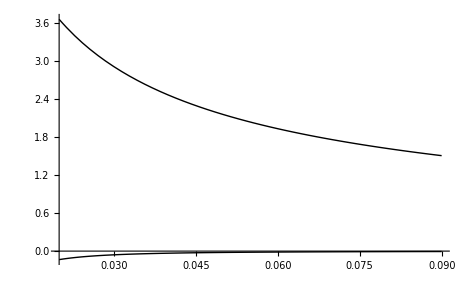

```mathematica
Plot[{𝒷E,(R/(Γ+(-R (℘γ/℧)(1-ω(-℘γ/℧)))-R))} /.  𝔤 -> 𝔤Index,{𝔤Index,0.02,0.09}]
```

```mathematica
ℵ=(ÞΓ^-ρ-1)
```

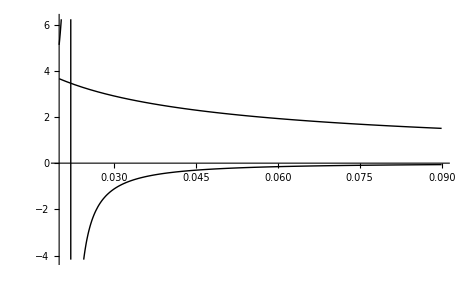

```mathematica
Plot[{𝒷E,((Γ/(R))-℘rtn(1-(℘γ/℧)(1-(-(℘γ/℧)ω))))^-1} /.  𝔤 -> 𝔤Index,{𝔤Index,0.02,0.09}]
```

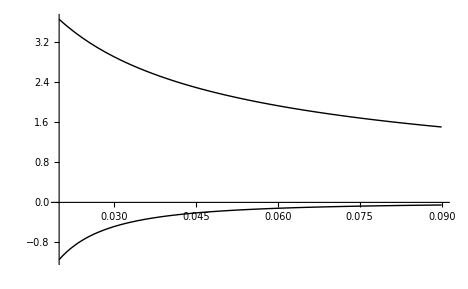

```mathematica
Plot[{𝒷E ,1/((γ-r)+ϑ(1+(γ/℧)(1-(γ/℧)ω)))}/. 𝔤 -> 𝔤Index,{𝔤Index,0.02,0.09}]
```

```mathematica
Manipulate[Block[{$PerformanceGoal="Quality",𝔤},𝔤=𝔤Slider;𝒷E],{{𝔤Slider,0.08,"𝔤"},0.07,0.09,0.005}]
```

```mathematica
𝒷E
```

1/(1+𝔤)1.1144 (-0.897344 (1+𝔤)+((0.+1. (1+(0.101142 √(1+200. (-1+0.974001 (1+𝔤)^2)))/(1+𝔤))) (1-τ))/(1+(0.101142 √(1+200. (-1+0.974001 (1+𝔤)^2)))/(1+𝔤)-(1.1144 (1-τ))/(1+𝔤))-((0.+1. (1+(0.101142 √(1+200. (-1+0.974001 (1+𝔤)^2)))/(1+𝔤))) (1-0.897344 (1+𝔤)-τ))/(1+(0.101142 √(1+200. (-1+0.974001 (1+𝔤)^2)))/(1+𝔤)-(1.1144 (1-τ))/(1+𝔤)))

```mathematica
rBase
```

0.03

```mathematica
𝔤Base
```

0.

```mathematica
??𝓂E
```

Global`𝓂E

𝓂E=(-((1+r) Severance (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)+(1+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤)) (1-Severance ℧))/(1-((1+r) (1-τ) (1-℧))/(1+𝔤)+((1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ) (1-℧))/(1+𝔤))

```mathematica
D[𝓂ENoSoi,r]
```

1/(-1-r+(1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)+(1+𝔤)/(1-℧))-((1+r) (-1+(1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)+(1+r) (((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)^2-((1-PDies) ((1+r)/(1+ϑ))^(-1+1/ρ))/((1+r) (1+ϑ) ρ)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)-((1+r) ((1+r)/(1+ϑ))^(-1+1/ρ) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(-1+1/ρ) (1-℧) ((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^(-1-ρ))/((1+𝔤) (1+ϑ) ρ ℧)))/(-1-r+(1+r) (1-((1-PDies) ((1+r)/(1+ϑ))^(1/ρ))/(1+r)) (1+(-1+((((1+r)/(1+ϑ))^(1/ρ) (1-℧))/(1+𝔤))^-ρ)/℧)^(1/ρ)+(1+𝔤)/(1-℧))^2

```mathematica
FindStableArm;
{𝓂Max,𝓂MaxMax}={2,4} 𝓂E;𝒸Max=cE[𝓂MaxMax];
Severance=0;
Manipulate[
Block[{$PerformanceGoal="Quality", r},
r=rSlider;If[((R) β)^(1/ρ)/Γ ≥  1||((R) β)^(1/ρ)/(R) ≥  1,Style[Text["Impatience Condition Not Satisfied."],24];Abort[]];
𝓂TargetDiagram[𝓂Max,𝓂MaxMax,𝒸Max]
],{{rSlider,rBase,"r"},rBase-0.025,rBase+.06,0.005}]
```

```mathematica
SetDirectory[NotebookDirectory[]];<<ManipulatePrepare.m;
```

NotebookDirectory::nosv: The notebook aepsi_shm is not saved.

SetDirectory::fstr: File specification $Failed is not a string of one or more characters.

NotebookDirectory::nosv: The notebook aepsi_shm is not saved.

SetDirectory::fstr: File specification $Failed is not a string of one or more characters.